```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]


pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 334 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,Parallel`Debug`Perfmon`,Parallel`Debug`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Integrate[ ρ x^2 , { x , -l/2 , l/2 } ]
Clear[ℐ]
ℐ = Integrate[ ρ x^2 , { x , -l/2 , l/2 } ]  /. ρ -> M/l
```

(l^3 ρ)/12

(l^2 M)/12

```mathematica
Clear[s]
s = { x[t] Cos[θ[t]] , x[t] Sin[θ[t]] }
```

{Cos[θ[t]] x[t],Sin[θ[t]] x[t]}

```mathematica
D[s, t]
```

{Cos[θ[t]] x'[t]-Sin[θ[t]] x[t] θ'[t],Sin[θ[t]] x'[t]+Cos[θ[t]] x[t] θ'[t]}

```mathematica
D[s, t] . D[s, t]
```

(Sin[θ[t]] x'[t]+Cos[θ[t]] x[t] θ'[t])^2+(Cos[θ[t]] x'[t]-Sin[θ[t]] x[t] θ'[t])^2

```mathematica
D[s, t] . D[s, t]  // Expand
```

Cos[θ[t]]^2 x'[t]^2+Sin[θ[t]]^2 x'[t]^2+Cos[θ[t]]^2 x[t]^2 θ'[t]^2+Sin[θ[t]]^2 x[t]^2 θ'[t]^2

```mathematica
D[s, t] . D[s, t]  // Expand  // Simplify
```

x'[t]^2+x[t]^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 M ( D[s, t] . D[s, t]  // Expand  // Simplify  ) + 1/2 ℐ θ'[t]^2  ;
T // pdConv
```

1/24 l^2 M ((∂θ(t))/(∂t))^2+1/2 M ((x(t))^2 ((∂θ(t))/(∂t))^2+((∂x(t))/(∂t))^2)

```mathematica
Clear[V]
V = 0
```

0

```mathematica
Clear[ℒ]
ℒ = T - V ;
ℒ // pdConv
```

1/24 l^2 M ((∂θ(t))/(∂t))^2+1/2 M ((x(t))^2 ((∂θ(t))/(∂t))^2+((∂x(t))/(∂t))^2)

```mathematica
Clear[q]
q = { x[t] , θ[t] }
```

{x[t],θ[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t ] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ]
```

-M x[t] θ'[t]^2+M x''[t]

2 M x[t] x'[t] θ'[t]+1/12 l^2 M θ''[t]+M x[t]^2 θ''[t]

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ] , t ] - D[ ℒ , q[[i]] ] == 0 , 
{ i , 1, 2 } ] // Simplify // TableForm
```

M x[t] θ'[t]^2==M x''[t]
M (24 x[t] x'[t] θ'[t]+l^2 θ''[t]+12 x[t]^2 θ''[t])==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

M (x[t] θ'[t]^2-x''[t])==0
-1/12 M (24 x[t] x'[t] θ'[t]+l^2 θ''[t]+12 x[t]^2 θ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
M-> 10 , 
l-> 1 
} ;
parameters // TableForm
```

M→10
l→1

```mathematica
eqs /. parameters // Expand // TableForm
```

10 x[t] θ'[t]^2-10 x''[t]==0
-20 x[t] x'[t] θ'[t]-(5 θ''[t])/6-10 x[t]^2 θ''[t]==0

```mathematica
Clear[ics]
ics = { 
x[0] ==  0.1 ,
x'[0] == 0.1 ,
θ[0] == 0 ,
θ'[0] == 0.1 
} ;
ics // TableForm
```

x[0]==0.1
x'[0]==0.1
θ[0]==0
θ'[0]==0.1

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 10 } ]]
```

{x[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[  Evaluate[ q /. solution[t] ]  , { t, 0, 10 }, PlotLabels-> q ]
```

-Graphics-

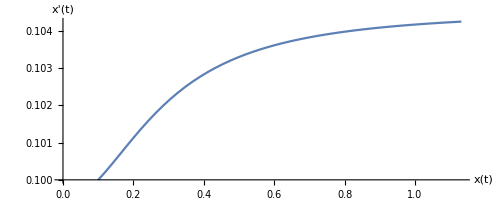

```mathematica
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, 10 } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]
```

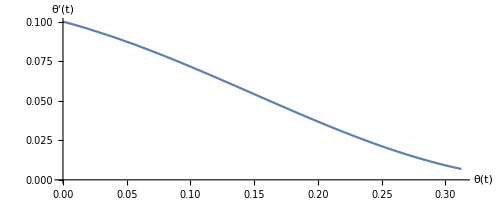

```mathematica
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, 10 }, AxesLabel-> { q[[2]] , D[q[[2]], t] } ]
```